```mathematica
ClearAll["Global`*"]
```

Path to the density profiles (“ density maps”)

```mathematica
PathMD="/Volumes/UNI/Densmaps_Version_v2_planar/";
```

## SAM 0 %

## FIRST : we plot all density profiles to determine the (integration) interval where the water density has a stable bulk value. In order to do so we store the density values as lists in separate variables: nWaterData0 and nSurfData0 for number density, WaterData0 and SurfData0 for mass density (of the surface with 0% -OH coverage).

Number Density

Store water mass density of SAM 0 % in nWaterdata0

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"ndens_NVT_sam0_water_ptensor_center.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
nWaterData0 = Take[input,{start+1,Length[input]}]; 
(* Divide by 3 (ONLY!) the density values to get density of molecules instead of particles *)
nWaterData0[[All,2]]=nWaterData0[[All,2]]/3;
```

Store the surface mass density of SAM 0 % in nSurfData0

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"ndens_SAM_sam0_water_ptensor_center.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
nSurfData0 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

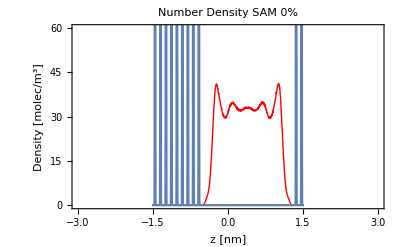

```mathematica
nWaterPlot0=ListPlot[nWaterData0,Joined->True,PlotStyle->{Red,Thick}];
nSurfPlot0=ListPlot[nSurfData0,Joined->True];
nPlot0=Show[nWaterPlot0,nSurfPlot0,PlotLabel->"Number Density SAM 0%",FrameLabel->{"z [nm]","Density [molec/m^3]"},Frame->True,PlotRange->{{-3,3.},{0,60}}]
```

### Mass Density

Store water mass density of SAM 0 % in Waterdata0

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam0_water_ptensor_center.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData0 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 0 % in SurfData0

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam0_water_ptensor_center.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData0 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

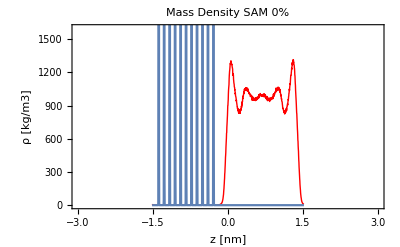

```mathematica
waterplot0=ListPlot[WaterData0,Joined->True,PlotStyle->{Red,Thick}];
surfplot0=ListPlot[SurfData0,Joined->True];
plotMass0=Show[waterplot0,surfplot0,PlotLabel->"Mass Density SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-3,3.},{0,1600}}]
```